# LaF3:Lm^(3+)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
theLanthanides={"Pr","Nd","Pm","Sm","Eu","Gd","Tb","Dy","Ho","Er","Tm"};
```

```mathematica
lnData=(#->Import[FileNameJoin[{NotebookDirectory[],#<>" in LaF3 - tiny.m"}]])&/@theLanthanides;
lnData=Association[lnData];
```

```mathematica
Get["../qplotter.m"]
```

```mathematica
Style[Subscript[1,1],Tiny]
```

1_1

```mathematica
BetterLabel[aLabel_]:=(
spinPart=StringTake[aLabel,{1}];
orbPart=StringTake[aLabel,{2}];
jayPart=StringTake[aLabel,{3,-1}];
Grid[{{Superscript["",spinPart],Subscript[orbPart,Style[jayPart,Small]]}},Spacings->{-0.1}]
)
```

```mathematica
BetterLabel["2L11/2"]
```

^2 | L_(11/2)

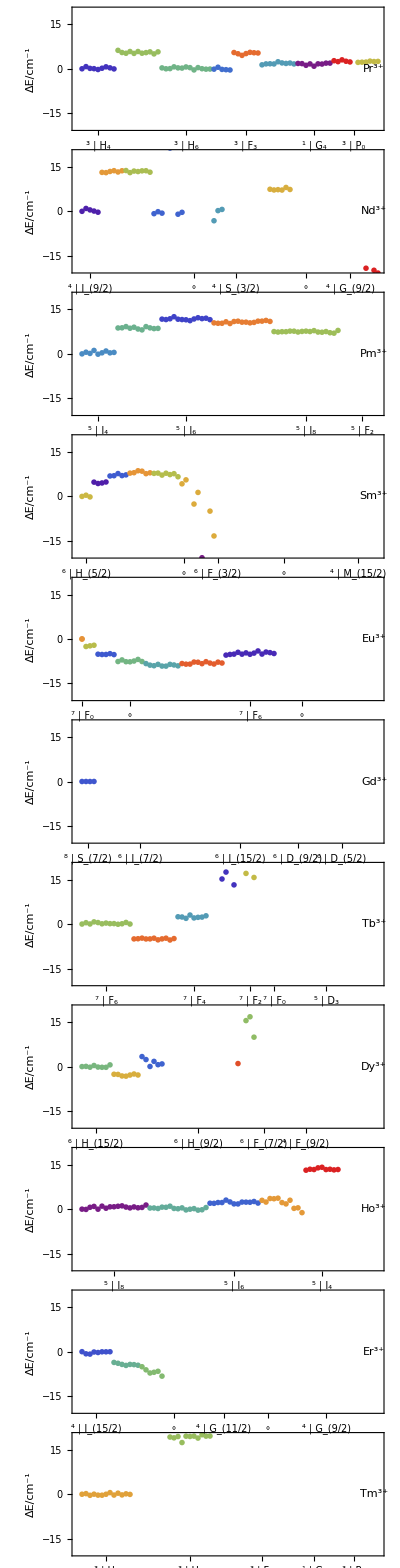

```mathematica
maxDiffs=75;
vRange=20;
plots=Table[(
lnD=lnData[ln];
eigenEnergies=lnD["eigenEnergies"];
carnallEnergies=lnD["carnallEnergies"];
simplerStateLabels=lnD["simplerStateLabels"];
eigenEnergies=eigenEnergies[[;;Length[carnallEnergies]]];
simplerStateLabels=simplerStateLabels[[;;Length[carnallEnergies]]];
diffs=eigenEnergies-carnallEnergies;
chooser=FreeQ[#,Missing[]]&/@carnallEnergies;
freecarnallEnergies=Pick[carnallEnergies,chooser];
freeeigenEnergies=Pick[eigenEnergies,chooser];
theLabels=Pick[simplerStateLabels,chooser];
diffs=Pick[diffs,chooser];
diffs=diffs[[;;Min[maxDiffs,Length[chooser]]]];
diffs=diffs-diffs[[1]];
theLabels=theLabels[[;;Min[maxDiffs,Length[chooser]]]];
theLabels=BetterLabel/@theLabels;
ListLabelPlot[diffs,theLabels,ImageSize->800,PlotMarkers->{"OpenMarkers",Small},AspectRatio->1/15,PlotRange->{All,{-vRange,vRange}},
Epilog->Text[Framed[Style[Superscript[ln,"3+"]],FrameMargins->4],
{Length[theLabels]-1,0},Background->White],FrameLabel->{None,"ΔE/cm^-1"}]
),
{ln,theLanthanides}];
plotMaster=Column[plots]
```

```mathematica
Export["~/Desktop/dmplot.pdf",plotMaster]
```

~/Desktop/dmplot.pdf

```mathematica
maxDiffs=75;
Manipulate[(
plots=Table[(
lnD=lnData[ln];
eigenEnergies=lnD["eigenEnergies"];
carnallEnergies=lnD["carnallEnergies"];
simplerStateLabels=lnD["simplerStateLabels"];
eigenEnergies=eigenEnergies[[;;Length[carnallEnergies]]];
simplerStateLabels=simplerStateLabels[[;;Length[carnallEnergies]]];
diffs=eigenEnergies-carnallEnergies;
chooser=FreeQ[#,Missing[]]&/@carnallEnergies;
freecarnallEnergies=Pick[carnallEnergies,chooser];
freeeigenEnergies=Pick[eigenEnergies,chooser];
theLabels=Pick[simplerStateLabels,chooser];
diffs=Pick[diffs,chooser];
diffs=diffs[[;;Min[maxDiffs,Length[chooser]]]];
theLabels=theLabels[[;;Min[maxDiffs,Length[chooser]]]];
ListLabelPlot[diffs,theLabels,ImageSize->800,PlotMarkers->"OpenMarkers",AspectRatio->1/15,PlotRange->{All,{-span,span}},Epilog->Text[Framed[Style[Superscript[ln,"3+"]]],{Length[theLabels]-1,0},Background->White],FrameLabel->{None,"ΔE/cm^-1"}]
),
{ln,theLanthanides}];
plotMaster=Column[plots]
)
,{{span,25},10,100,1},
TrackedSymbols:>{span}]
```

```mathematica
Dynamic[{span,maxDiffs}]
```

```mathematica
plotIndex=Table[(
plots=Table[(
lnD=lnData[ln];
eigenEnergies=lnD["eigenEnergies"];
carnallEnergies=lnD["carnallEnergies"];
simplerStateLabels=lnD["simplerStateLabels"];
eigenEnergies=eigenEnergies[[;;Length[carnallEnergies]]];
simplerStateLabels=simplerStateLabels[[;;Length[carnallEnergies]]];
diffs=eigenEnergies-carnallEnergies;
chooser=FreeQ[#,Missing[]]&/@carnallEnergies;
freecarnallEnergies=Pick[carnallEnergies,chooser];
freeeigenEnergies=Pick[eigenEnergies,chooser];
theLabels=Pick[simplerStateLabels,chooser];
diffs=Pick[diffs,chooser];
diffs=diffs[[;;Min[maxDiffs,Length[chooser],Length[diffs]]]];
theLabels=theLabels[[;;Min[maxDiffs,Length[chooser],Length[diffs]]]];
ListLabelPlot[diffs,theLabels,ImageSize->800,PlotMarkers->"OpenMarkers",AspectRatio->1/15*span/10,PlotRange->{All,{-span,span}},Epilog->Text[Framed[Style[Superscript[ln,"3+"]]],{Length[theLabels]-1,0},Background->White],FrameLabel->{None,"ΔE/cm^-1"}]
),
{ln,theLanthanides}];
plotMaster=Column[plots];
({span,maxDiffs}->plotMaster)
)
,{span,10,100,10},{maxDiffs,50,150,10}];
```

```mathematica
plotIndex=Association[Flatten[plotIndex,1]];
```

```mathematica
Manipulate[plotIndex[{span,maxDiffs}],{span,10,100,10},{maxDiffs,50,150,10}]
```

```mathematica
Length[simplerStateLabels]
```

91